# Lab_Work_5

# 1.

```mathematica
На основе проделанных выше вычислений подберите примеры,подтверждающие справедливость следующих утверждений:
```

```mathematica
а)Пробел выполняет роль знака умножения
```

```mathematica
3 5
3*5
```

15

15

```mathematica
б)Введение дополнительных пробелов не изменяет результата вычислений
```

```mathematica
3 5
3          5
```

15

15

```mathematica
2+7
2+        7
```

9

9

```mathematica
3/7.
3      /7.
```

0.428571

0.428571

```mathematica
в)Целые,рациональные и иррациональные числа считаются заданными точно. Поэтому в выражениях,содержащих только такие числа,при обработке производятся лишь возможные упрощения,но сами они остаются точными и преобразуются в числа,заданные приближенно,только по команде пользователя.
```

```mathematica
2/3
```

2/3

```mathematica
17^(1/2)
```

√17

```mathematica
г) Действительные числа,содержащие десятичную точку,считаются заданными приближенно. Поэтому выражения,в которые входят действительные числа,вычисляются при обработке секции без специальной команды.
```

```mathematica
17.          ^(1/2)
```

4.12311

```mathematica
3      /7.
```

0.428571

```mathematica
д) Для изменения стандартного порядка выполнения операций используются скобки
```

```mathematica
3 (6 +  11 )
```

51

# 2.

```mathematica
а)С помощью функции N вычислить 17^(1/2) с точностью до 200 значащих цифр. Проверить точность полученного результата с помощью функции Precision
```

```mathematica
(*N[expr, n] - даёт цифровое значение expr с точностью n
Precision - дает эффективное количество цифр точности в числе x*)
```

```mathematica
N[Sqrt[17], 200]
```

4.1231056256176605498214098559740770251471992253736204343986335730949543463376215935878636508106842966845440409392141416153014208404158683630795481457469069776770232664362408630877905675723857082255214

```mathematica
Precision[N[Sqrt[17], 200]]
```

200.

```mathematica
б) Найдите приближенное значение числа e^(Pi*√163)точностью до 40 значащих цифр. Вычислите,на сколько полученный результат отличается от ближайшего к нему целого числа. Для стандартного округления чисел в системе используется Round[a1]
```

```mathematica
(*Round[x] - даёт целое число, ближайшее к x*)
a1 = N[E^(Pi*Sqrt[163]),40]
a2 =Round[a1]
a1 - a2
```

2.625374126407687439999999999992500725972×10^17

262537412640768744

-7.499274028×10^-13

```mathematica
в) Вычислите:
```

```mathematica
(10*((10.8*10^3)/300)^(1/2) + 4)^(1/3)
```

4.

```mathematica
(10^-24 10^12)/10^-14 √(32768/2^9)
```

800

```mathematica
г) Последовательно введите выражения:5>3;5<2;и посмотрите,что выдает математика при их обработке.Затем определите,справедливо или нет равенство Pi^E>E^Pi.Найдите численные значения левой и правой частей неравенства и убедитесь в правильности полученного результата.
```

```mathematica
5>3
5<2
```

True

False

```mathematica
Pi^E>E^Pi
N[Pi^E]
N[E^Pi]
```

False

22.4592

23.1407

# 3.

```mathematica
а) Решить уравнения
```

```mathematica
(*CTRL+2 -> квадратный корень
NSolve [expr, vars] - пытается найти численные приближения к решениям системы expr уравнений или неравенств для переменных vars*)
```

```mathematica
NSolve[√(k+2)+4 k == 4, k]
```

{{k→0.597111}}

```mathematica
NSolve[k^3-3  k^2+5 == 0, k]
```

{{k→-1.1038},{k→2.0519-0.565236 ⅈ},{k→2.0519+0.565236 ⅈ}}

```mathematica
б)Решить системы уравнений
```

```mathematica
(*CTRL+6 - верхний индекс*)
```

```mathematica
NSolve[{k^2+k y+y^2==1, k^3+k^2 y+k y^2+y^3==4}, {k,y}]
```

{{k→-1.-1.41421 ⅈ,y→-1.+1.41421 ⅈ},{k→-1.+1.41421 ⅈ,y→-1.-1.41421 ⅈ},{k→1.6838+0.133552 ⅈ,y→-0.683802-1.13355 ⅈ},{k→1.6838-0.133552 ⅈ,y→-0.683802+1.13355 ⅈ},{k→-0.683802-1.13355 ⅈ,y→1.6838+0.133552 ⅈ},{k→-0.683802+1.13355 ⅈ,y→1.6838-0.133552 ⅈ}}

```mathematica
NSolve[{k-y^2+3z == 34, k+y-z==-1, -k+2y+3z ==4}, {k,y,z}]
```

{{k→9.25-10.2317 ⅈ,y→-3.5+4.09268 ⅈ,z→6.75-6.13901 ⅈ},{k→9.25+10.2317 ⅈ,y→-3.5-4.09268 ⅈ,z→6.75+6.13901 ⅈ}}

```mathematica
в)Придумайте уравнение или систему полиномиальных уравнений и найдите ее численное решение
```

```mathematica
NSolve[2*k^3+6*k^2+k-3 == 0, k]
```

{{k→-2.58114},{k→-1.},{k→0.581139}}

# 4.

```mathematica
Используя функцию FindRoot,найти решения следующих уравнений
```

```mathematica
(*FindRoot[f1==f2,{x, x0}] - иищет численное решение уравнения f1=f2. Поиск корня начинается от x0*)
```

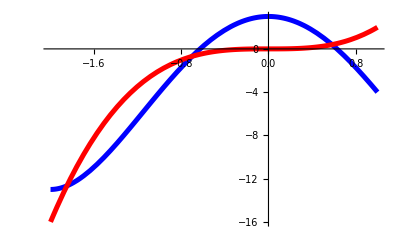

```mathematica
Plot [{k^4-8 k^2+3, 2 k^3}, {k,-2,1},PlotStyle->{{Thickness[0.009], RGBColor[0,0,1]}, {Thickness[0.009], RGBColor[1,0,0]}}]
```

```mathematica
(*Корни уравнения находятся приблизительно у k=-1.9, k=-0.7, k=0.6*)
```

```mathematica
FindRoot[k^4-8 k^2+3==2 k^3,{k,-1.9}]
FindRoot[k^4-8 k^2+3==2 k^3,{k,-0.8}]
FindRoot[k^4-8 k^2+3==2 k^3,{k,0.5}]
```

{k→-1.8502}

{k→-0.700886}

{k→0.58301}

# 5.

```mathematica
Найдите решение следующего дифференциального уравнения на заданном отрезке
```

```mathematica
(*NDSolve[enqs,u,{x,xmin,xmax}] - находит численное решение обыкновенных дифференциальных уравнений уравнений для функции u с независимой переменной х в диапазоне от xmin до xmax*)
```

```mathematica
s=NDSolve[{y''[k]+k^2 y[k]-1==0,y[0]==0,y'[0]==1},y,{k,0,4}]
```

{{y→InterpolatingFunction[…]}}

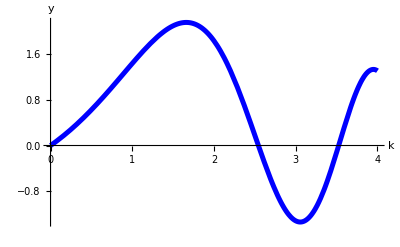

```mathematica
(*Используем полученное решение для построения графика*)
Plot[y[k]/.s, {k,0,4}, AxesLabel->{"k", "y"}, PlotStyle->{RGBColor[0,0,1], Thickness[0.009]}]
```

```mathematica
а) Найдите на заданном отрезке корни уравнения y(k)=0
```

```mathematica
sol1=FindRoot[(y[k]/.s)==0, {k,0}]
sol2=FindRoot[(y[k]/.s)==0, {k,2.4}]
sol3=FindRoot[(y[k]/.s)==0, {k,3.4}]
```

{k→0.}

{k→2.54324}

{k→3.52562}

```mathematica
б)Найдите значения производной y`(k) в точках,где y(k)=0
```

```mathematica
(* D[f,x] - дает частную производную df/dx *)
```

```mathematica
D[y[k]/.sol,k]/.sol1 
D[y[k]/.sol,k]/.sol2
D[y[k]/.sol,k]/.sol3
```

{1.}

{-4.08962}

{4.70107}

```mathematica
в)Выберите одну из точек,в которых производная функции y(k) равна нулю,и вычислите значение функции в этой точке
```

```mathematica
sol4 = FindRoot[D[y[k]/.s,k]==0,{k,1.4}]
```

{k→1.66088}

```mathematica
y[k] /.s[[1]]/.sol4
```

2.15037

```mathematica
г)С помощью функции FindMinimum найдите точки,в которых функция y(k) имеет локальный минимум или максимум,и сравните полученные результаты со значениями,найденными в пункте в)
```

```mathematica
(*FindMinimum[f,x] - находит локальный минимум в f,начиная с автоматически выбранной точки. Данная функция имеет похожую структуру с FindRoot*)
```

```mathematica
FindMinimum[y[k]/.s,{k,2.8}]
```

{-1.33679,{k→3.0556}}

```mathematica
FindMaximum[y[k]/.s,{k,1.6}] (*результат == результату в пункте в), т.к. в точке минимума(максимума) производная = 0 *)
```

{2.15037,{k→1.66088}}

# 6.

```mathematica
a)Задайте произвольные численные значения параметров a,b,c,d,e в следующих зависимостях
```

```mathematica
y(k)== a+b*k+c*k^2+d*k^3+e*k^4
y(k)== a+b*k+c*Sin[k]+d*Cos[k]
y(k)== a+b*k+c*Sin[k]+d*Cos[2*k]
y(k)== a*Sin[k]+b*cos[k]+c*Sin[2*k]+d*Cos[2*k]
Используя функцию Table,определите список численных данных,каждый элемент которого содержит два соответствующих элемента (x,y).Область изменения х и шаг выберите самостоятельно.С помощью функции Random внесите в каждой точке х случайное возмущение del y.
(*Измеряется координата тела в заданные моменты времени. В результате должна получиться таблица численных данных. Рандом отвечает за генерацию погрешностей измерений
Table[expr, n] - генерирует список n копий expr*)
```

```mathematica
result = Table[{k,(3+6k+4Sin[k]+7Cos[2*k])(1+Random[Real, {-0.1, 0.1}])}, {k,0,8,0.25}]
```

{{0.,9.79956},{0.25,10.9321},{0.5,11.4715},{0.75,10.5106},{1.,9.58778},{1.25,8.9767},{1.5,8.28439},{1.75,10.4883},{2.,14.7764},{2.25,17.7288},{2.5,21.5253},{2.75,27.6173},{3.,30.0139},{3.25,30.7912},{3.5,28.4928},{3.75,27.8668},{4.,23.1077},{4.25,18.8656},{4.5,18.7422},{4.75,21.7327},{5.,25.5749},{5.25,25.8908},{5.5,31.2332},{5.75,36.8678},{6.,44.5824},{6.25,51.7893},{6.5,52.1666},{6.75,52.8613},{7.,43.9131},{7.25,45.438},{7.5,48.5532},{7.75,46.85},{8.,45.9864}}

```mathematica
б) Изобразите полученные точки на координатной плоскости
```

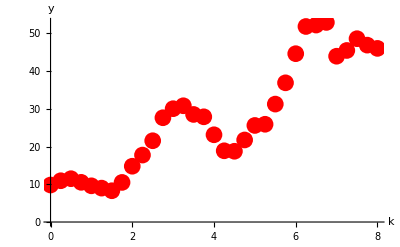

```mathematica
(*Чтобы увидеть зависимость y=y(k), переносим численные значения на график*)
resultPlot=ListPlot[result, PlotStyle->{ Red,PointSize[0.03]}, AxesLabel->{"k", "y"}]
```

```mathematica
в) С помощью функции Fit найдите наилучшую кривую,аппроксимирующую численные данные
```

```mathematica
(*Для нахождения наилучших, с точки зрения метода наименьших квадратов, значения коэффициентов используется функция Fit
Fit[data, {f1,...,fn}, {x,y,...}] - находит соответствие a1*f1+...+an*fn списку data для функций f1,...,fn переменных x,y,...*)
y1=Fit[result, {1,k,Sin[k], Cos[2*k]},k]
```

3.00617+6.04572 k+7.84161 Cos[2 k]+3.96504 Sin[k]

```mathematica
(*Найденные значения коэффициентов близки к тем, которые были использовваны при генерации численных данных. Для сравнения попробуем провести через экспериментальные точки наилучшую кривую, уравнение которой представляет собой, например полином 4 степени*)
```

```mathematica
y2=Fit[result, {1,k,k^2, k^3, k^4},k]
```

6.24781+10.3803 k-4.26558 k^2+0.959969 k^3-0.0634195 k^4

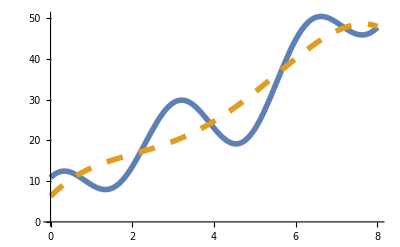

```mathematica
plot2 =Plot[{y1,y2}, {k,0,8},PlotStyle->{{Thickness[0.01]},{Thickness[0.01],Dashing[{0.03}]}}]
```

```mathematica
г) На одной координатной плоскости изобразите найденную кривую вместе с экспериментальными точками
```

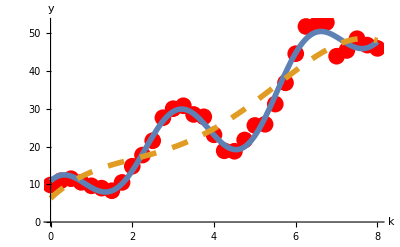

```mathematica
Show[resultPlot, plot2]
```

```mathematica
(*Как видим, сплошная кривая, полученная при использовании реальной зависимости y=y(k), гораздо лучше соответствует экспериментальным результатам, чем полиномиальная зависимость (кривая, изображённая штриховой линией)*)
```